# Similarity Index of 1D Cellular Automata

## Inheritance properties in CA increasing definitions

Erick Jesse Angeles Lopez

Usually the names of rules depend on the configuration, such as ECA or B3/S23 in life, but all rules can be defined as a decimal number. Since here we are going to study rules that belong to different spaces, it is necessary to distinguish the origin of each one of them. To start, we will use the following notation:

```mathematica
Subscript[rule, states,neighbourhood]
```

## Dimensionless Cellular Automaton

### One state

A CA that has a single state and a single neighbor can only have one possible transition rule, rule .

-Graphics-

### Two states

For 2 states, we can generate the following  rules:

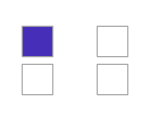
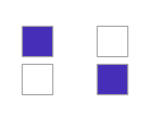
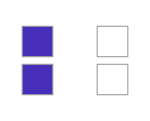
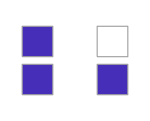
-Graphics- | -Graphics- | -Graphics- | -Graphics-

Applying a color inversion we obtain that  and  have the same behavior.

Rule  share similarities with .

Rule  and  are unknown till now.

### Three states

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

: Same like the rule .

: This is a rule with a period-2 attractor that is not reversible. Similar to .

: This rule has 2 fixed-point attractors. Similar to .

: This rule has 1 fixed-point attractor. Similar to .

: This rule has 1 periodic attractor and 1 fixed-point attractor. Similar to  and .

: Rule  has the same behavior as , as it is an attractor whose period is defined by the number of states, and it is its own inverse rule.

: Rule  has the same behavior as .

### Up to seven states

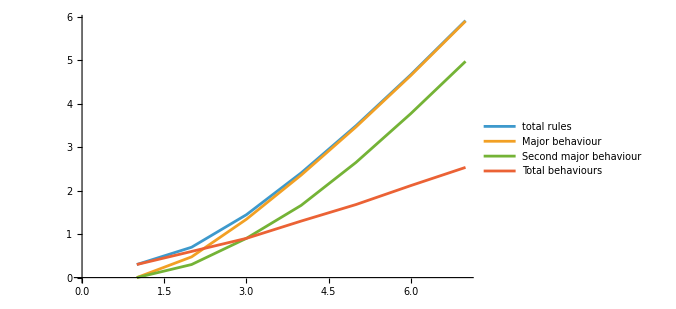

### Up to seven states

Behaviors per states. We can observe that all rules with  states are a subset of the rules with  states, with the difference that the new state is assigned a transition to 0

```mathematica
{{-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-}}
```

### State transitions

There exists a mapping between rules that allows us to move between CA spaces. That is, we can move from rule  a la  simply by adding a new state that points to state 0

Rules {0,0,0,0,0,0,0}:

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Rules {0,0,0,0,0,0,1}:

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Rules {0,0,0,0,1,1,2}:

-Graphics- | -Graphics- | -Graphics- | -Graphics-

We need to conditions to apply the inverse process:

The last state transition to 0

None state transition to the last state

But there are exceptional cases that do not seem to satisfy this, for example, rule , which if we remove the last transitions we obtain the following rules:

-Graphics-

But rules ,  do not belong to the list of unique behaviors; however, we can apply the inverse function to find the representative of that behavior and discover where that pattern comes from.

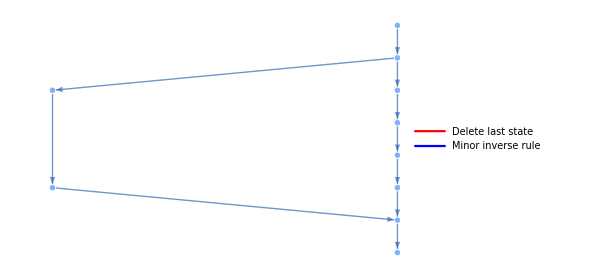

```mathematica
Module[{
vectors={{0,0,1,1,1},{0,1,1,1},{1,1,1},{0,0,0},{0,0},{0},{0,0,2,0},{0,2,0},{0,1,1},{1,1}},
edges={{0,0,1,1,1}->{0,1,1,1},{0,1,1,1}->{1,1,1},{1,1,1}->{0,0,0},{0,0,0}->{0,0},{0,0}->{0},{0,1,1,1}->{0,0,2,0},{0,0,2,0}->{0,2,0},{0,2,0}->{0,1,1},{0,1,1}->{1,1},{1,1}->{0,0}},
colores={({0,0,1,1,1}->{0,1,1,1})->Red,({1,1}->{0,0})->Blue,({0,1,1,1}->{1,1,1})->Red,({0,0,0}->{0,0})->Red,({0,0}->{0})->Red,({0,0,2,0}->{0,2,0})->Red,({0,1,1}->{1,1})->Red,({1,1,1}->{0,0,0})->Blue,({0,1,1,1}->{0,0,2,0})->Blue,({0,2,0}->{0,1,1})->Blue}},
Legended[LayeredGraph[
Graph[
edges,
EdgeStyle->colores,
VertexShapeFunction->(Inset[
ArrayPlot[{#2},
ColorRules->colorRules,
ImageSize->{Length[#2]*20,20},
Mesh->True,
MeshStyle->Gray,
ImagePadding->0,
PlotRangePadding->0
],#1]&),
VertexSize->{0.01,0.25}],
ImageSize->{450,Automatic}
],LineLegend[colores[[All,2]],{"Delete last state","Minor inverse rule"}]]
]
```

### Hypergraph of transitions

## One dimension Cellular Automaton

Now we take a look in 2 states and 2 neighbors rules:

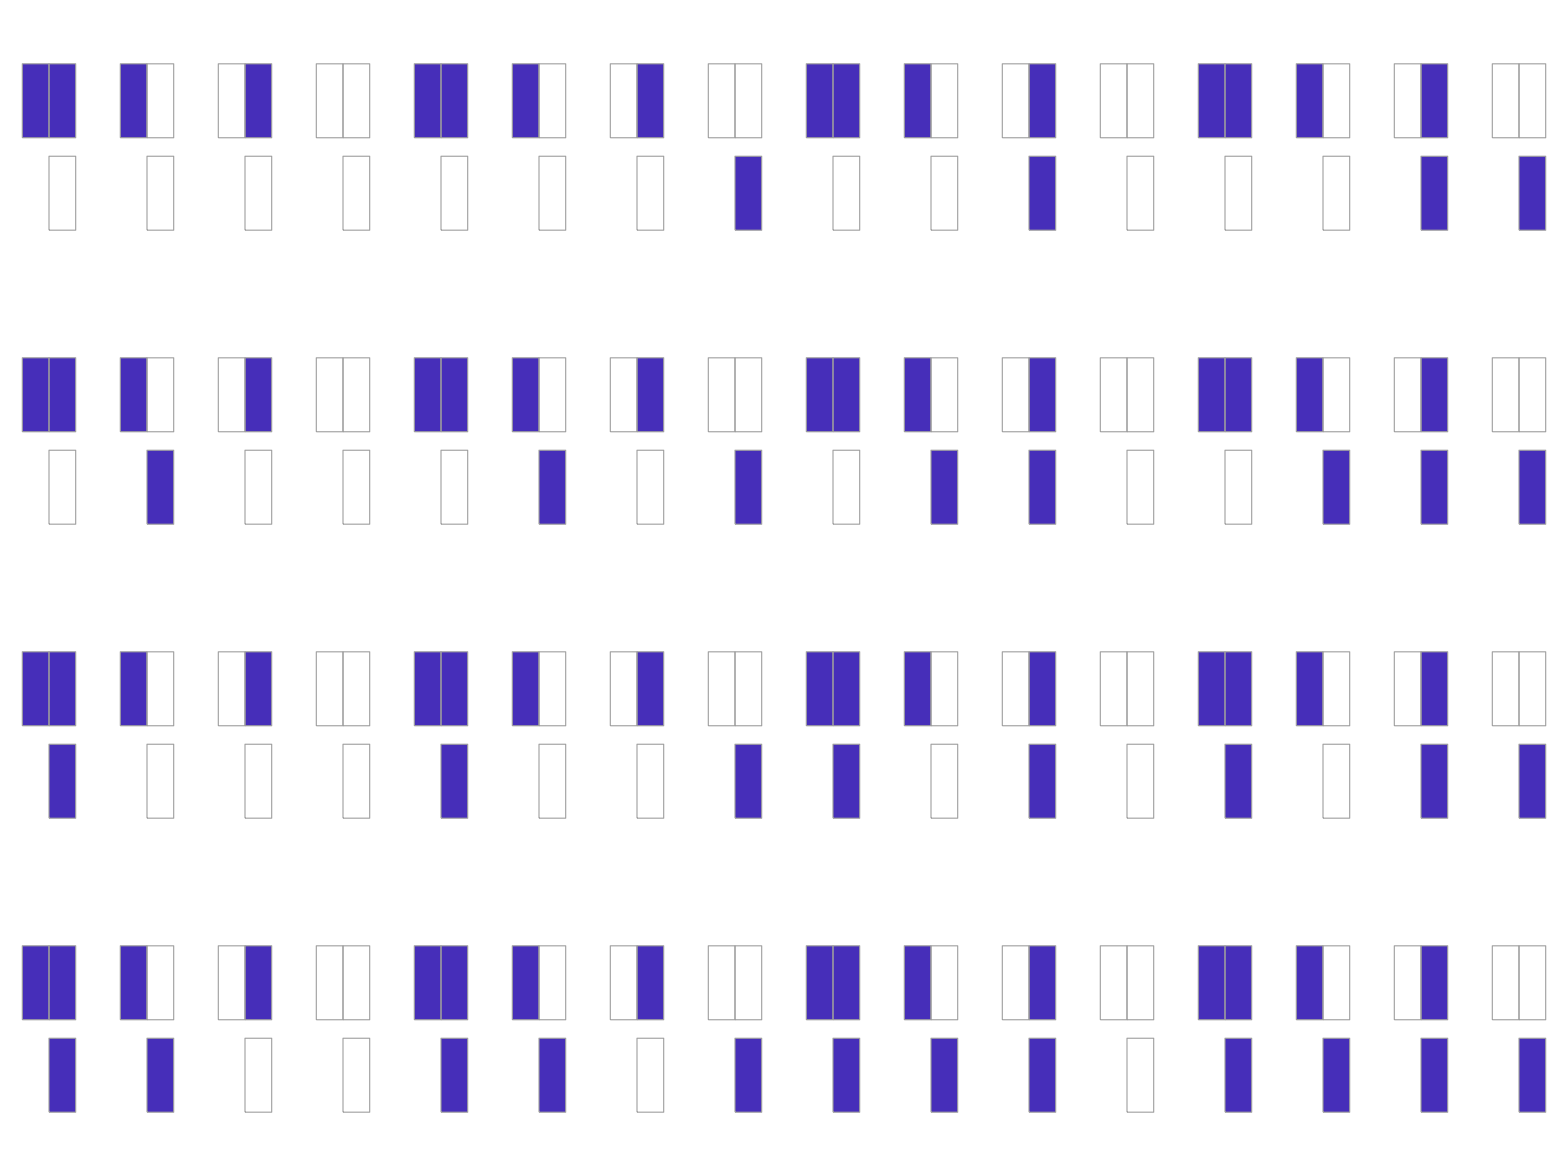

We can reduce by state inversion:

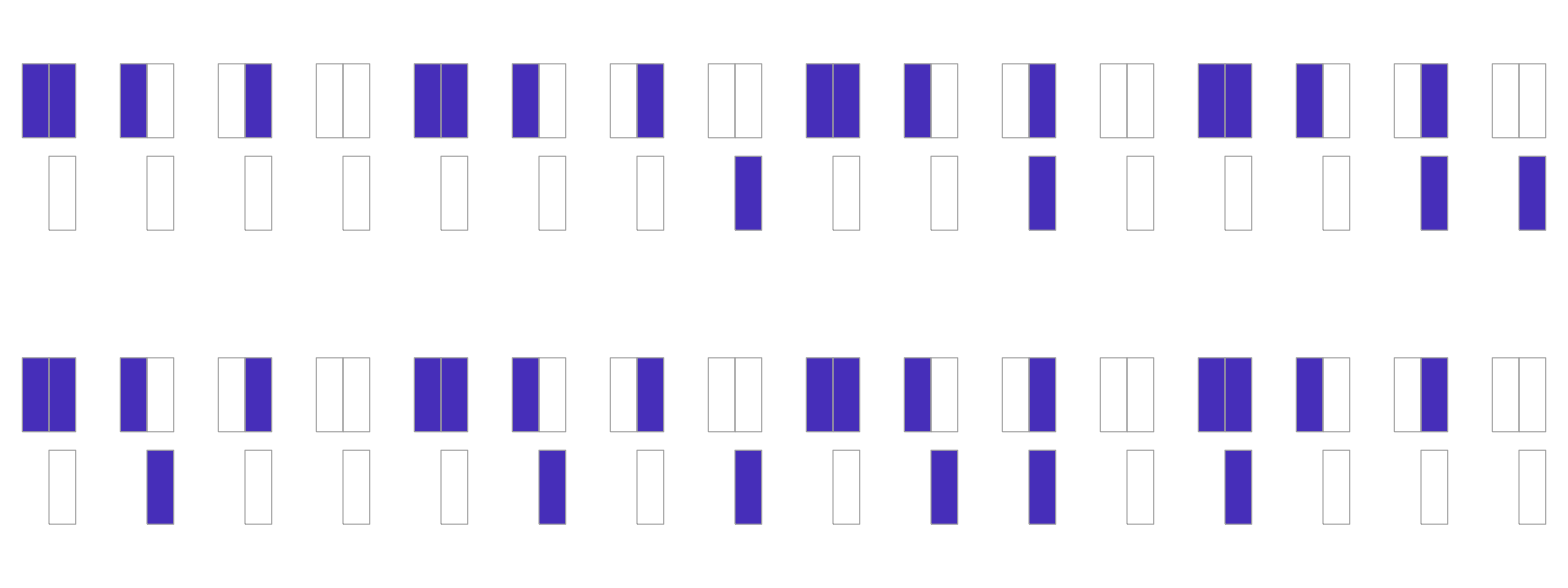

Additionally, we require a function to search to the symmetric rule:

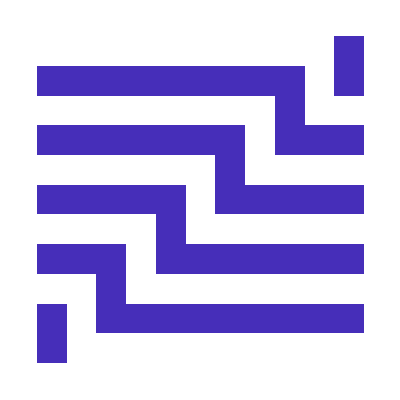
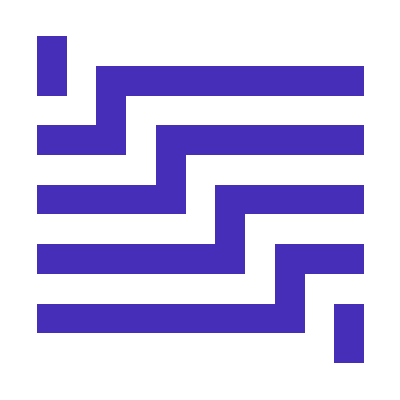

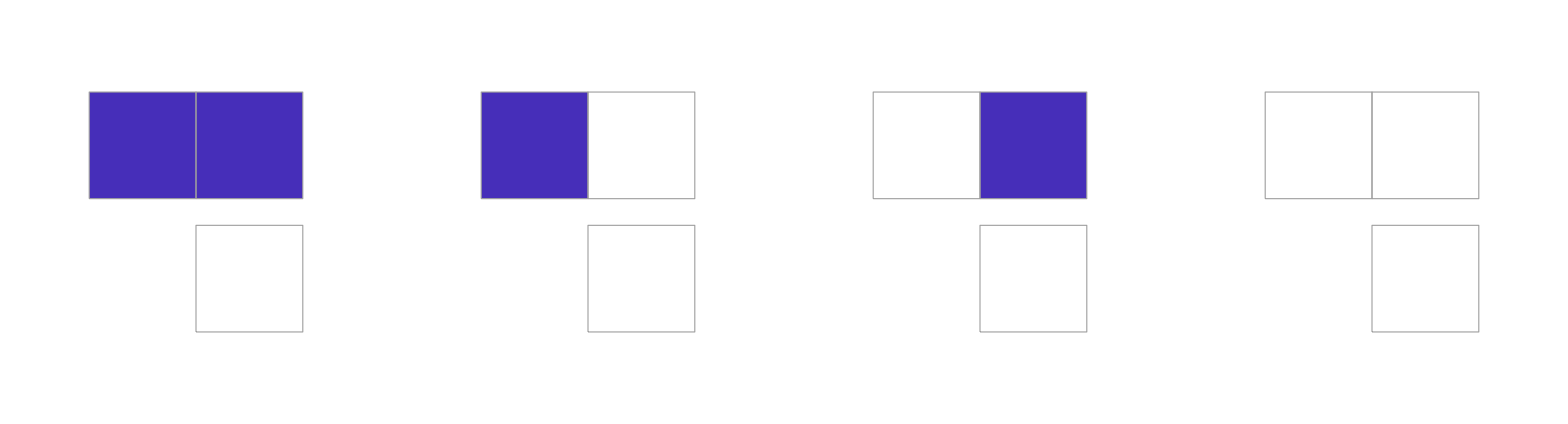
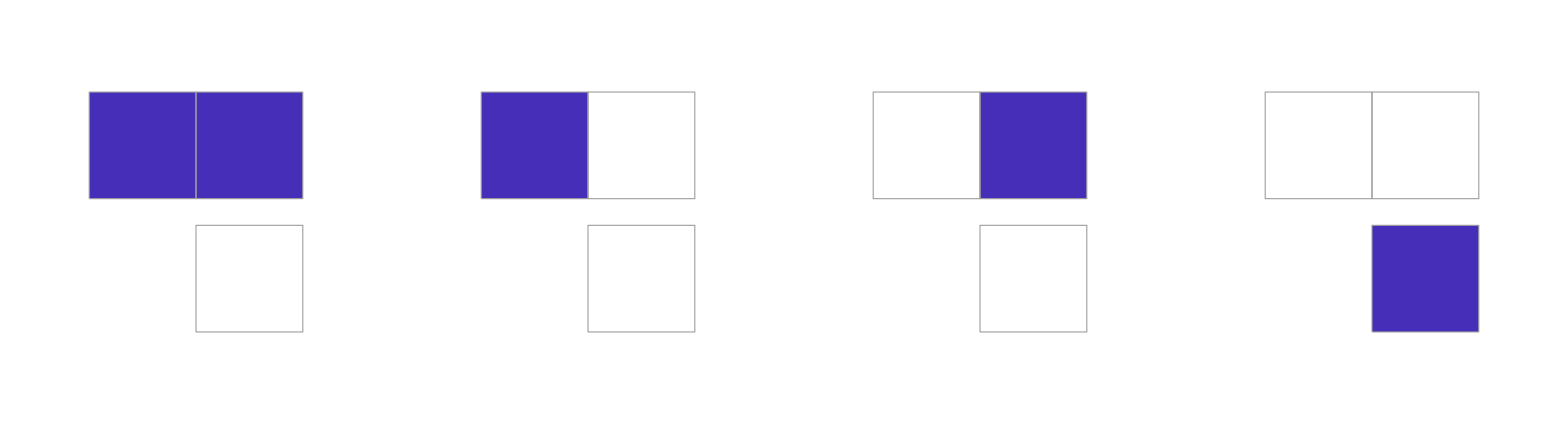
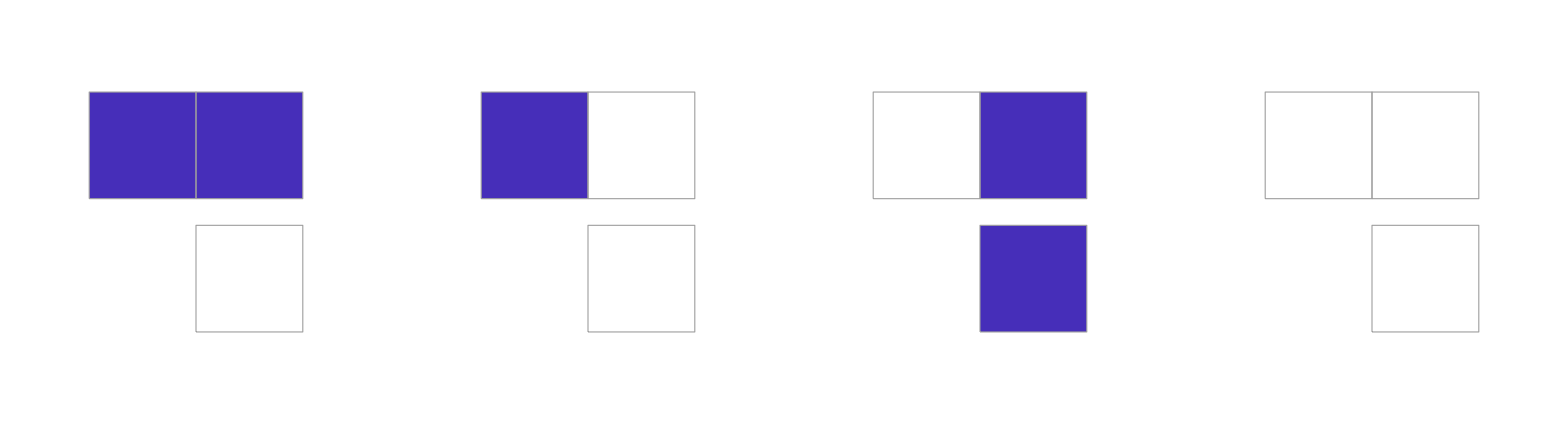
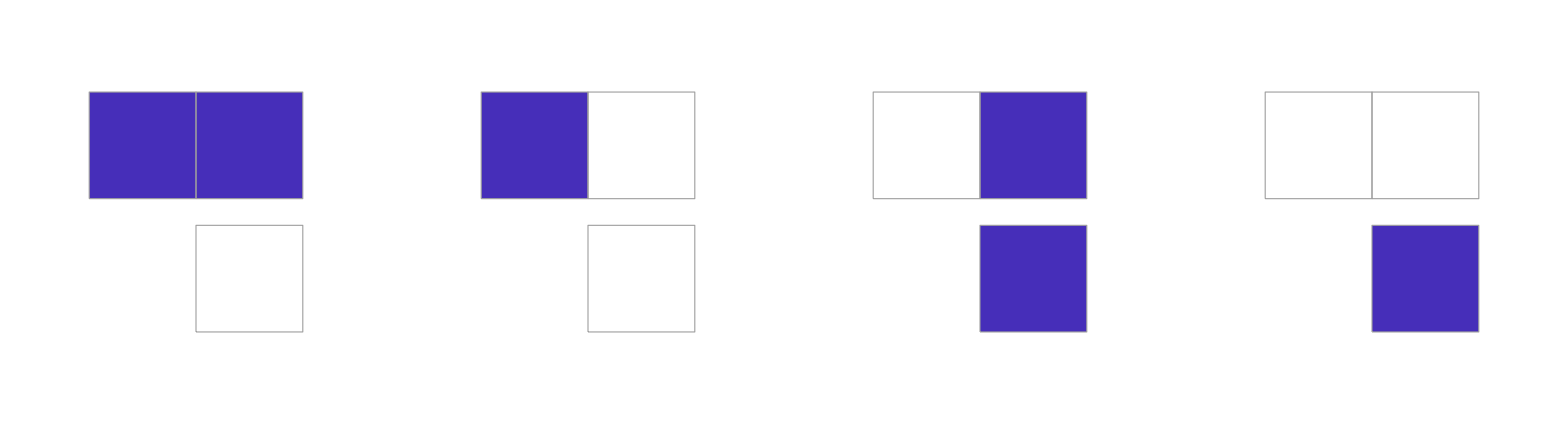
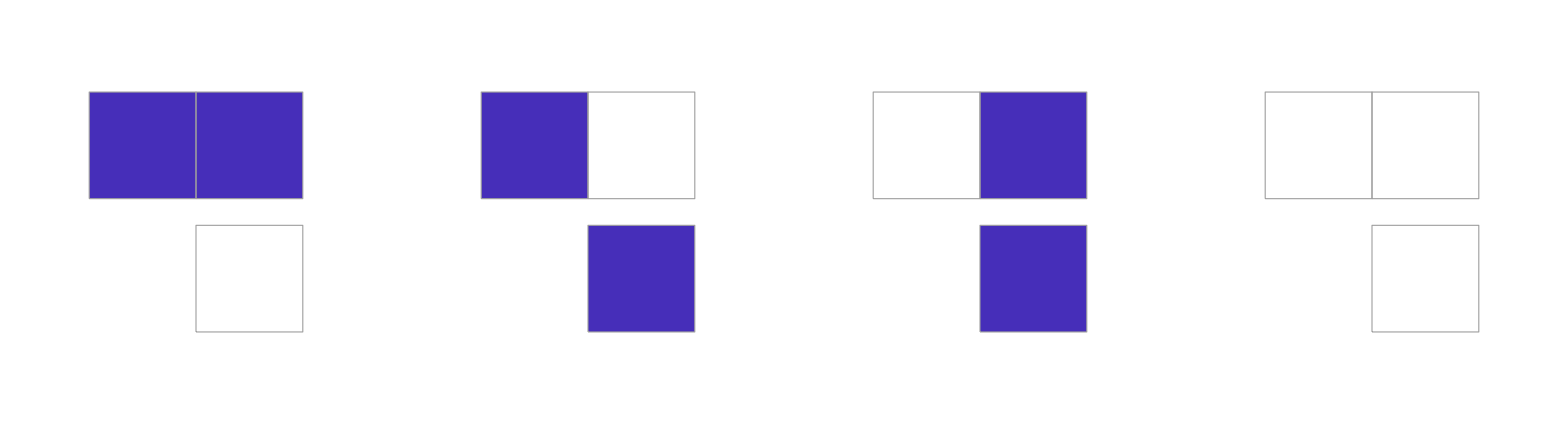
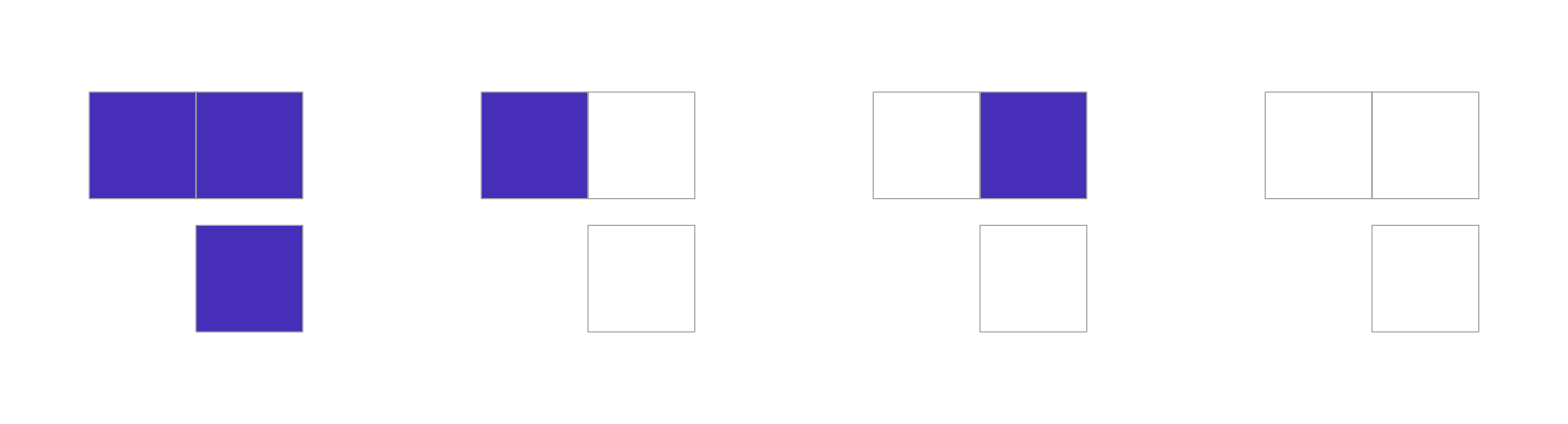

### Neighbor reduction

Rule  has no dependency in the neighbors as  and

Rule  depends on his left neighbor as rule

Rule  depends on his right neighbor as rule

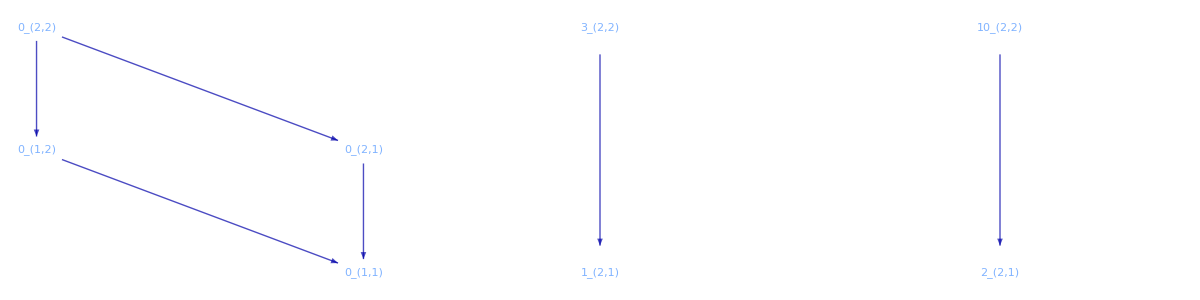

### New behaviors

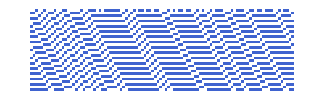
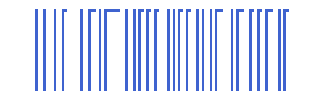
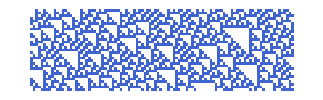
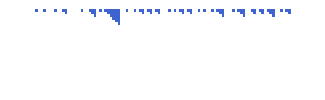

## Next steps

We can build a graph that connect the rules from different spaces.

We can apply reduction by state or by neighbor

We can transform a rule by state inversion or symmetry

For 2 states and 2 neighbors we find only 4 new behaviors but for 3 states and 2 neighbor there are more than 1700 unclassified behaviors.The next association should reduce to 1200 rules.

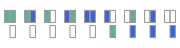
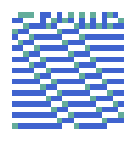
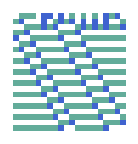
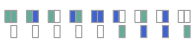

# Thanks